```mathematica
(* Routine to produce solution *)
FindSol:=(i=0;interstep={};
{minim,minsolrep}=Monitor[FindMinimum[normedrel.normedrel,{nvars,nvars/.subnc}//Transpose,WorkingPrecision->prec,PrecisionGoal->Infinity,AccuracyGoal->prec/2,MaxIterations->50,Method->Automatic,EvaluationMonitor:>(i++;norm=normedrel.normedrel//N;If[i>MyMaxIterations,Throw["Too big step"]];AppendTo[interstep,nvars])],Row@{"Step: " ,i,",   Minim: ",norm}];AppendTo[NoSteps,i];AppendTo[Steps,interstep]);
SilentFindSol:=(i=0;
interstep={};{minim,minsolrep}=FindMinimum[normedrel.normedrel,{nvars,nvars/.subnc}//Transpose,WorkingPrecision->prec,PrecisionGoal->Infinity,AccuracyGoal->prec/2,MaxIterations->50,Method->Automatic,EvaluationMonitor:>(i++;If[i>MyMaxIterations,Throw["Too big step"]];AppendTo[interstep,nvars])];AppendTo[NoSteps,i];AppendTo[Steps,interstep]);
```

```mathematica
(* Iteration procedure *)
Iteratemyver[syt_]:=Block[{},
pp=pmin;qq=1;
step:=qq/base^pp;
(* starting the procedure *)
ΛLast=Λvals[[-1]];
Monitor[
While[ΛLast>Λtarget,If[step<10^-20,Print[{syt,step//N,Λvals//N}];Break[],
Λnew=Max[ΛLast-step,Λtarget];
normedrel=InterpEqns[Λnew];
Which[
Catch[SilentFindSol]==="Too big step",
pp=pp+1,
i>5,
sol[Λnew]=minsolrep;
AppendTo[Λvals,Λnew]
,
True,
sol[Λnew]=minsolrep;
AppendTo[Λvals,Λnew];
If[pp>pmin,qq=qq+Δq;If[qq==base,qq=1;pp=pp-1]];
];
ΛLast=Λvals[[-1]];
]],
Row@{"Current Λ history is: ",Λvals//N,"current Λ is: ",ΛLast//N, "   step is: ",step//N}];
];
```

```mathematica
base=2;pmin=3;RecoverySpeed=1/3;prec=80;interpord=40;

SolutionFromSYTmyver[SYT_]:=Block[{},
NoSteps={};
Steps={};
λT=SYT;
λ=SYT//ToYD;
GenerateQsystem[λ];
LargeΛExpansion;
SubleadingOrders;
GenerateEqnsForNumerics;
SolveAtΛ0;
GenerateSolsFromAsymptotics;
Λvals=Λvals0;
(* the previous line resets Λvals - a record for which Λ solution was already found *)
Iteratemyver[SYT];
Steps=Steps[[2;;]];
Steps={Λvals[[#]],vars2nvars/.Λ->Λvals[[#]]/.(Thread[nvars->#]&)/@Steps[[#]]}&/@Range[Length[Steps]];
{Λvals,vars2nvars/.Λ->Λvals[[#]]/.sol[Λvals[[#]]]&/@Range[1,Length[Λvals]],(u/.Table[NSolve[YQa[a,0]/.vars2nvars/.Λ->Λvals[[#]]/.sol[Λvals[[#]]],u],{a,Length[λ]-1}])&/@Range[1,Length[Λvals]]}
];
```

```mathematica
yd={5,3};
L=Total[yd];
rigs=ModestoRiggedConfig[L,#]&/@ModesConfig[yd];
syts=ToSYT/@rigs;
```

```mathematica
MyMaxIterations=12;
NoStepsAll={};
StepsAll={};
lazyans=Module[{ans},ans=SolutionFromSYTmyver[#];AppendTo[NoStepsAll,NoSteps];AppendTo[StepsAll,Steps];ans]&/@syts;
(*Monitor[(AppendTo[lazyans,SolutionFromSYTmyver[#]];syt=#)&/@syts,syt];*)
```

```mathematica
MyMaxIterations=5;
NoStepsAll={};
StepsAllCORRECT={};
lazyansCORRECT=Module[{ans},ans=SolutionFromSYTmyver[#];AppendTo[NoStepsAll,NoSteps];AppendTo[StepsAll,Steps];ans]&/@syts;
(*Monitor[(AppendTo[lazyans,SolutionFromSYTmyver[#]];syt=#)&/@syts,syt];*)
```

35

28

{{1,22},{8,11,28},{17,19},{24,26},{30,32},{31,33}}

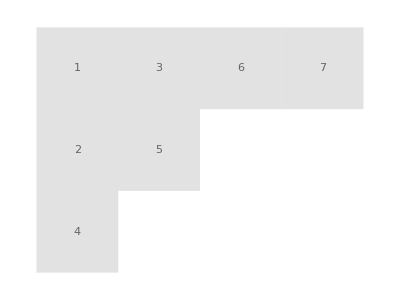
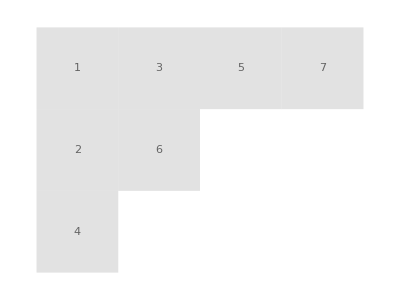
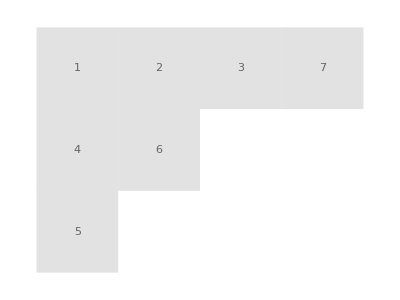
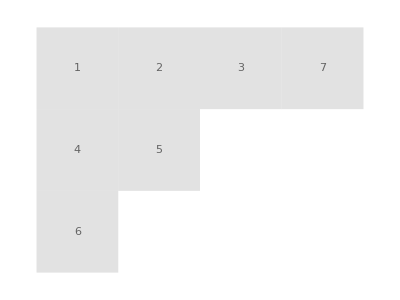
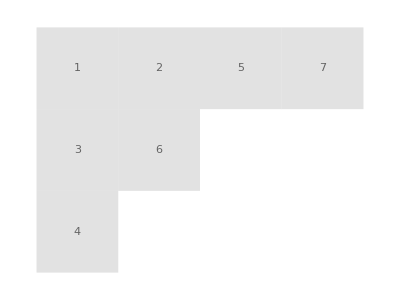
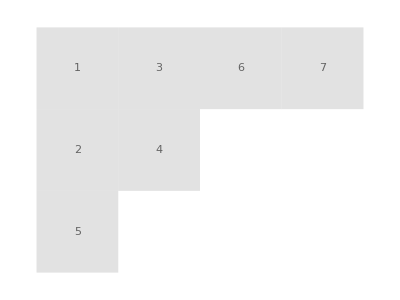
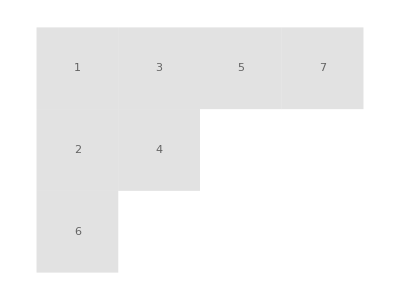
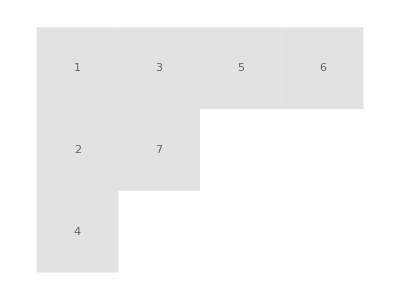

```mathematica
a=1;
Round[lazyans[[All,3,-1]],10^-3]//N//Length
Round[lazyans[[All,3,-1]],10^-3]//N//DeleteDuplicates//Length

repeats=If[#[[2]]>1,{#[[1]]//Flatten,Position[Round[lazyans[[All,3,-1,a]],10^-3]//N,#[[1]]]//Flatten},Nothing]&/@Tally[Round[lazyans[[All,3,-1,a]],10^-3]//N];
repeatlist=repeats[[All,2]]

showSYT/@ToSYT/@rigs[[#]]&/@repeatlist
```

```mathematica
lazyansone=SolutionFromSYTmyver[syts[[20]]];
```

```mathematica
NoSteps;

lazyansone[[1]]//N;
%//ListPlot;

deltalambda=Table[lazyansone[[1,i]]-lazyansone[[1,i+1]],{i,Length[lazyansone[[1]]]-1}]//ListPlot;

Table[Table[pdist[Steps[[no]][[i]],Steps[[no]][[i+1]],2],{i,Length[Steps[[no]]]-1}],{no,Length[Steps]}];
%//ListLinePlot[#,PlotRange->All,PlotLegends->lazyansone[[1]]]&;
```

```mathematica
(*Distance function, L^p*)
pdist[vec1_,vec2_,p_,uast_:1]:=Total[Table[Abs[vec1[[i]]-vec2[[i]]]^p*uast/Sqrt[Abs[vec1[[i]]*vec2[[i]]+1]],{i,1,Length[vec1]}]]^(1/p)
```

```mathematica
(*Finding distances between solutions (for different rigged configurations, numbered by no1, no2) for chosen lists of Lambda values; lambdalist is a descending list*)
coeffStraightlines[positions_,lambdalist_,lambda_]:=Module[{baselambda,baseposition,foundpositions},baselambda=SelectFirst[lambdalist//Reverse,#>=lambda&];
baseposition=Position[lambdalist,baselambda][[1,1]];
foundpositions=If[lambda!=lambdalist[[-1]],positions[[baseposition]]+(positions[[baseposition+1]]-positions[[baseposition]])/(lambdalist[[baseposition+1]]-baselambda)*(lambda-baselambda),positions[[-1]]]]

distanceChooseLambda[ans_,no1_,no2_,lambdalist_]:=pdist[coeffStraightlines[ans[[no1,2,All,All,2]],ans[[no1,1]],#],coeffStraightlines[ans[[no2,2,All,All,2]],ans[[no2,1]],#],2]&/@lambdalist
```

```mathematica
repeatlistsets=Subsets[#,{2}]&/@repeatlist;
Distanceslistssets=Map[(Lambdalistshared=Sort[Intersection[lazyans[[#[[1]],1]],lazyans[[#[[2]],1]]],Greater];distanceChooseLambda[lazyans,#[[1]],#[[2]],Lambdalistshared])&,repeatlistsets,{2}];
dist=Map[Part[#,-6;;-1]&,Distanceslistssets,{2}]//Round
```

{{{26,14,7,3,2,0}},{{34,15,6,2,1,0},{77,32,12,4,2,0},{115,48,18,7,3,0}},{{41,18,7,3,1,0}},{{53,21,8,3,1,0}},{{45,19,7,3,1,0}},{{22,11,5,2,1,0}}}

```mathematica
Lambdalist=lazyans[[4,1]];
distanceChooseLambda[lazyans,4,7,Lambdalist]//Round;
```

```mathematica
no=30;
deltalambda=Table[lazyans[[no,1,i]]-lazyans[[no,1,i+1]],{i,Length[lazyans[[no,1]]]-1}];
Table[pdist[lazyans[[no,2,i,All,2]],lazyans[[no,2,i+1,All,2]],2],{i,Length[lazyans[[no,2]]]-1}]//Round;
```

```mathematica
PlotQmyver[avalues_,color_:{Blue,PointSize[0.01]}]:=Map[Replace[x_:>{Re[x],Im[x]}],avalues,{2}]//ListPlot[#,PlotStyle->color,ImageSize->Medium,PlotRange->All]&;

ColorCodes1=Darker/@{Blue,Green,Yellow,Pink,Cyan,Magenta,Red,Orange,Gray,Black};
ColorCodes2=Lighter/@{Blue,Green,Yellow,Pink,Cyan,Magenta,Red,Orange,Gray,Black};

ManipulatePlotmyver[values1_,values2_,Λvals1_,Λvals2_]:=Manipulate[
Row[{Row[{"Λs=",{SetAccuracy[Λvals1[[k]],3],SetAccuracy[Λvals2[[kk]],3]}}],Show[{PlotQmyver@@@Reverse[Table[{{values1[[k]][[a]],values2[[kk]][[a]]},{{ColorCodes1[[a]],PointSize@Sizes[[a]]},{ColorCodes2[[a]],PointSize@Sizes[[a]]}}},{a,Length[λ]-1}]]}]}],{{k,1,Row[Prepend[Table[ColorCodes1[[i]],{i,Length[λ]-1}],"no1 "]]},1,Length[Λvals1],1},{{kk,1,Row[Prepend[Table[ColorCodes2[[i]],{i,Length[λ]-1}],"no2 "]]},1,Length[Λvals2],1}];
```

```mathematica
no1=4;
no2=7;
ManipulatePlotmyver[-lazyans[[no1,3]]+1,-lazyans[[no2,3]]+1,lazyans[[no1,1]],lazyans[[no2,1]]]
```

Show::shx: No graphical objects to show.

```mathematica
size[vec_]:=Total[Abs[vec]^2]^(1/2)
sizes=GroupBy[Flatten[Transpose/@Map[{#[[1]],size/@(#[[2]]//Values)}&,lazyans],1],First][[All,All,2]];
```

```mathematica
comp=1;
lists=Table[If[i!=comp,{comp,i},Nothing],{i,Length[lazyans[[All,3,-1]]]}];
lists={{4,7}};
lists=Subsets[Range[1,Length[lazyans]],{2}];
showSYT/@ToSYT/@rigs[[#]]&/@lists;

normdistancesprev=Module[{Ltest},{(Ltest=Sort[Intersection[lazyans[[#[[1]],1]],lazyans[[#[[2]],1]]],Greater])[[2;;]],
Table[pdist[lazyans[[#[[1]],2,Position[lazyans[[#[[1]],1]],i][[1,1]]]]//Values,lazyans[[#[[2]],2,Position[lazyans[[#[[2]],1]],i][[1,1]]]]//Values,2]
/Max[sizes[Ltest [[Position[Ltest,i][[1,1]]-1]]]]
,{i,Ltest[[2;;]]}]}//Transpose]&/@lists;
normdistances=Module[{Ltest},{Ltest=Sort[Intersection[lazyans[[#[[1]],1]],lazyans[[#[[2]],1]]],Greater],
Table[pdist[lazyans[[#[[1]],2,Position[lazyans[[#[[1]],1]],i][[1,1]]]]//Values,lazyans[[#[[2]],2,Position[lazyans[[#[[2]],1]],i][[1,1]]]]//Values,2]
/Max[sizes[i]]
,{i,Ltest}]}//Transpose]&/@lists;
distances=Module[{Ltest},{Ltest=Sort[Intersection[lazyans[[#[[1]],1]],lazyans[[#[[2]],1]]],Greater],
Table[
pdist[lazyans[[#[[1]],2,Position[lazyans[[#[[1]],1]],i][[1,1]]]]//Values,lazyans[[#[[2]],2,Position[lazyans[[#[[2]],1]],i][[1,1]]]]//Values,2]
,{i,Ltest}]
}//Transpose]&/@lists;
```

```mathematica
test=GroupBy[Flatten[distances,1],First][[All,All,2]];
Table[{i,Min[test[i]]},{i,test//Keys}]//ListPlot;
```

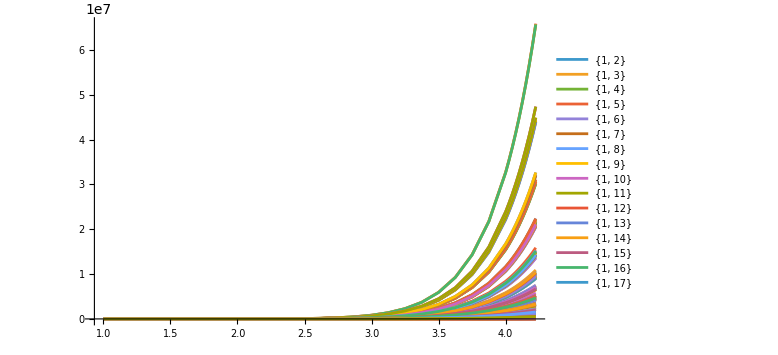

```mathematica
(*plotdist=#[[1;;-1]]&/@normdistances;*)
distances//ListLinePlot[#,PlotLegends->ToString/@lists,ImageSize->Large,PlotRange->All]&
```

```mathematica
repeatlist=repeats[[All,2]].08
```

{{.08,22 .08},{8 .08,11 .08,28 .08},{17 .08,19 .08},{24 .08,26 .08},{30 .08,32 .08},{31 .08,33 .08}}

```mathematica
comp=1;
val=Range[1,Length[lazyans]];
val={comp,22};
```

```mathematica
(*soltest={lazyans[[comp,1]],StepsAll[[comp]][[All,-1]]}//Transpose;*)
coeffinterp[comp_]:=AssociationThread[StepsAll[[comp,All,1]],StepsAll[[comp,All,2,1]]];

lazyanscoeff[v_]:=AssociationThread[lazyansCORRECT[[v,1]],lazyansCORRECT[[v,2]]];
Lambdashared[comp_,v_]:=Sort[Intersection[lazyans[[comp,1]],lazyansCORRECT[[v,1]]],Greater];
```

```mathematica
disttocomppolinterp=Table[{i,pdist[coeffinterp[comp][i]//Values,lazyanscoeff[v][i]//Values,2]},{v,val},{i,Lambdashared[comp,v]}];
```

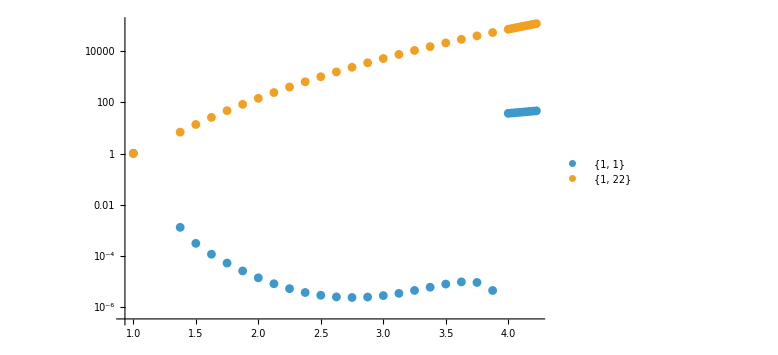

```mathematica
plotdist=#[[1;;-1]]&/@disttocomppolinterp;
plotdist//ListLogPlot[#,PlotLegends->ToString/@Table[{comp,i},{i,val}],ImageSize->Large,PlotRange->All]&
```

```mathematica
disttocomppolinterp[[All,-1]]
```

{{1,0.637202441383921606002509146572974167376192613155548845591464506662944881264937},{1,0.637202441383921606002509146572974167376191313738313336141086057166265828621247},{1,0.637202441383921606002509146572974167376191313738313336141086057244744097545532}}

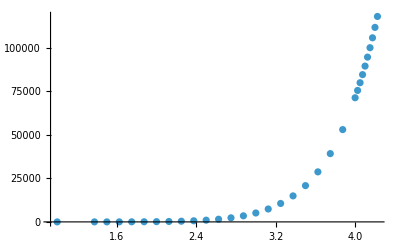

```mathematica
Table[{i,pdist[coeffinterp[1][i]//Values,coeffinterp[22][i]//Values,2]},{i,Lambdashared[1,22]}]//ListPlot[#,PlotRange->All]&
```

```mathematica
no1=1;
no2=22;
Manipulate[{(Replace[x_:>{Re[x],Im[x]}])/@(u/.Table[NSolve[YQa[a,0]/.StepsAll[[no1,i,2,1]]],{a,Length[λ]-1}][[1]]),(Replace[x_:>{Re[x],Im[x]}])/@(u/.Table[NSolve[YQa[a,0]/.StepsAll[[no2,j,2,1]]],{a,Length[λ]-1}][[1]]),(Replace[x_:>{Re[x],Im[x]}])/@(lazyansCORRECT[[no1,3,k,1]]),(Replace[x_:>{Re[x],Im[x]}])/@(lazyansCORRECT[[no2,3,l,1]])}//ListPlot[#,PlotRange->All,PlotStyle->{Green,Blue,Red,Yellow}]&,{{i,1,"green.Interp1" },1,Length[StepsAll[[no1]]],1},{{j,1,"blue.interp22" },1,Length[StepsAll[[no2]]],1},{{k,1,"red.real1" },1,Length[lazyansCORRECT[[no1,3]]],1},{{l,1,"yellow.real22" },1,Length[lazyansCORRECT[[no2,3]]],1}]
```

```mathematica
Manipulate[{Module[{},nvarsfuncCORRECT={lazyansCORRECT[[rigg1]][[1]],(nvars2vars/.Λ->#[[1]]/.#[[2]])&/@(lazyansCORRECT[[rigg1]][[1;;2]]//Transpose)};({nvarsfuncCORRECT[[1]],nvarsfuncCORRECT[[2,All,polno]]//Values}//Transpose)],Module[{},nvarsfuncCORRECT={lazyansCORRECT[[rigg2]][[1]],(nvars2vars/.Λ->#[[1]]/.#[[2]])&/@(lazyansCORRECT[[rigg2]][[1;;2]]//Transpose)};({nvarsfuncCORRECT[[1]],nvarsfuncCORRECT[[2,All,polno]]//Values}//Transpose)]}//ListPlot[#,PlotLegends->{rigg1,rigg2},PlotRange->All]&,{rigg1,1,Length[lazyansCORRECT],1},{rigg2,1,Length[lazyansCORRECT],1},{polno,1,Length[nvars],1}]
```

```mathematica
Manipulate[{Module[{},nvarsfuncCORRECT={lazyansCORRECT[[rigg1]][[1]],(nvars2vars/.Λ->#[[1]]/.#[[2]])&/@(lazyansCORRECT[[rigg1]][[1;;2]]//Transpose)};({nvarsfuncCORRECT[[1]],nvarsfuncCORRECT[[2,All,polno]]//Values}//Transpose)],Module[{},nvarsfunc={lazyans[[rigg2]][[1]],(nvars2vars/.Λ->#[[1]]/.#[[2]])&/@(lazyans[[rigg2]][[1;;2]]//Transpose)};({nvarsfunc[[1]],nvarsfunc[[2,All,polno]]//Values}//Transpose)]}//ListPlot[#,PlotLegends->{rigg1,rigg2},PlotRange->All]&,{rigg1,1,Length[lazyansCORRECT],1},{rigg2,1,Length[lazyans],1},{polno,1,Length[nvars],1}]
```

```mathematica
Manipulate[{Module[{},nvarsfunc={lazyans[[soln]][[1]],(nvars2vars/.Λ->#[[1]]/.#[[2]])&/@(lazyans[[soln]][[1;;2]]//Transpose)};({nvarsfunc[[1]],nvarsfunc[[2,All,polno]]//Values}//Transpose)],Module[{},
Subnc[Λ0_,minterpord_]:=
Thread[Rule[nvars,Round[Sum[(nvarsfunc[[2,1;;interpfrom]][[-j]]//Values)Product[If[j==j2,1,(Λ0-nvarsfunc[[1,1;;interpfrom]][[-j2]])/(nvarsfunc[[1,1;;interpfrom]][[-j]]-nvarsfunc[[1,1;;interpfrom]][[-j2]])],{j2,minterpord}],{j,minterpord}],10^-prec]]];
{nvarsfunc[[1,#]]&/@Range[interpfrom+1,Length[nvarsfunc[[1]]]],(Subnc[nvarsfunc[[1,#]],manyinterpor]&/@Range[interpfrom+1,Length[nvarsfunc[[1]]]])[[All,polno]]//Values}//Transpose]}//ListPlot[#,PlotLegends->(nvarsfunc[[2,1,polno]]//Keys),PlotRange->All]&,{soln,1,Length[lazyans],1},{polno,1,Length[nvars],1},{interpfrom,10,Length[lazyans[[soln,1]]]-1,1},{manyinterpor,1,interpfrom-1,1}]
```

```mathematica
Manipulate[Show[{Module[{},nvarsfunc={lazyans[[soln]][[1]],(nvars2vars/.Λ->#[[1]]/.#[[2]])&/@(lazyans[[soln]][[1;;2]]//Transpose)};({nvarsfunc[[1]],nvarsfunc[[2,All,polno]]//Values}//Transpose)],Module[{},
Subnc[Λ0_,minterpord_]:=
Thread[Rule[nvars,Round[Sum[(nvarsfunc[[2,1;;interpfrom]][[-j]]//Values)Product[If[j==j2,1,(Λ0-nvarsfunc[[1,1;;interpfrom]][[-j2]])/(nvarsfunc[[1,1;;interpfrom]][[-j]]-nvarsfunc[[1,1;;interpfrom]][[-j2]])],{j2,minterpord}],{j,minterpord}],10^-prec]]];
{nvarsfunc[[1,#]]&/@Range[interpfrom+1,Length[nvarsfunc[[1]]]],(Subnc[nvarsfunc[[1,#]],manyinterpor]&/@Range[interpfrom+1,Length[nvarsfunc[[1]]]])[[All,polno]]//Values}//Transpose]}//ListPlot[#,PlotRange->All,PlotStyle->{Blue,Black}]&,{Module[{},nvarsfuncCORRECT={lazyansCORRECT[[soln]][[1]],(nvars2vars/.Λ->#[[1]]/.#[[2]])&/@(lazyansCORRECT[[soln]][[1;;2]]//Transpose)};({nvarsfuncCORRECT[[1]],nvarsfuncCORRECT[[2,All,polno]]//Values}//Transpose)],Module[{},nvarsfuncCORRECT={lazyansCORRECT[[comp]][[1]],(nvars2vars/.Λ->#[[1]]/.#[[2]])&/@(lazyansCORRECT[[comp]][[1;;2]]//Transpose)};({nvarsfuncCORRECT[[1]],nvarsfuncCORRECT[[2,All,polno]]//Values}//Transpose)]}//ListLinePlot[#,PlotLegends->{soln,comp},PlotStyle->Opacity[0.5]]&],{soln,1,Length[lazyans],1},{polno,1,Length[nvars],1},{interpfrom,10,Length[lazyans[[soln,1]]]-1,1},{manyinterpor,1,interpfrom-1,1},{comp,1,Length[lazyans[[soln,1]]]-1,1}]
```

FilterRules::rep: 1.02475 is not a valid replacement rule.

First::normal: Nonatomic expression expected at position 1 in First[1.02475].

First::normal: Nonatomic expression expected at position 1 in First[-1.20565].

FilterRules::rep: -1.20565 is not a valid replacement rule.

OptionValue::rep: -1.20565 is not a valid replacement rule.

OptionValue::rep: 1.02475 is not a valid replacement rule.

OptionValue::rep: -1.20565 is not a valid replacement rule.

General::stop: Further output of OptionValue::rep will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[«1»],].

Join::heads: Heads System`ListPlotsDump`modelData and List at positions 1 and 2 are expected to be the same.

FilterRules::rep: Join[System`ListPlotsDump`modelData[AllOptions],{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→False,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,«4»}] is not a valid replacement rule.

ReplaceAll::reps: {System`ListPlotsDump`modelData[DependencyValues]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

OptionValue::rep: System`ListPlotsDump`modelData[AllOptions] is not a valid replacement rule.

OptionValue::optnf: Option name Axes not found in defaults for System`ListPlotsDump`modelData[AllOptions].

OptionValue::rep: System`ListPlotsDump`modelData[AllOptions] is not a valid replacement rule.

OptionValue::optnf: Option name Ticks not found in defaults for System`ListPlotsDump`modelData[AllOptions].

ReplaceAll::reps: {System`ListPlotsDump`modelData[DependencyValues]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

MapThread::mptd: Object Axes at position {2, 1} in MapThread[If[Visualization`Utilities`AxisObjectQ[#1],#2,#2]&,{Axes,Ticks}] has only 0 of required 1 dimensions.

Join::heads: Heads List and System`ListPlotsDump`modelData at positions 1 and 2 are expected to be the same.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[«1»],].

```mathematica
Manipulate[Module[{nvarsfunc,nvarsfuncCORRECT,nvarsfunccomp,nvarsfuncsoln,Subnc},
nvarsfunc={lazyans[[soln]][[1]],(nvars2vars/.Λ->#[[1]]/.#[[2]])&/@(lazyans[[soln]][[1;;2]]//Transpose)};
nvarsfuncCORRECT={lazyansCORRECT[[soln]][[1]],(nvars2vars/.Λ->#[[1]]/.#[[2]])&/@(lazyansCORRECT[[soln]][[1;;2]]//Transpose)};
nvarsfunccomp={lazyansCORRECT[[comp]][[1]],(nvars2vars/.Λ->#[[1]]/.#[[2]])&/@(lazyansCORRECT[[comp]][[1;;2]]//Transpose)};
nvarsfunccomp=Table[Interpolation[{nvarsfunccomp[[1]],nvarsfunccomp[[2,All,polno,2]]}//Transpose][x],{x,nvarsfuncCORRECT[[1]]}];
nvarsfuncsoln={lazyansCORRECT[[soln]][[1]],(nvars2vars/.Λ->#[[1]]/.#[[2]])&/@(lazyansCORRECT[[soln]][[1;;2]]//Transpose)};
nvarsfuncsoln=Table[Interpolation[{nvarsfuncsoln[[1]],nvarsfuncsoln[[2,All,polno,2]]}//Transpose][x],{x,nvarsfuncCORRECT[[1]]}];
Subnc[Λ0_,interpfrom_,nopoints_]:=
Thread[Rule[nvars,Round[Sum[(nvarsfuncCORRECT[[2,1;;interpfrom]][[-j]]//Values)Product[If[j==j2,1,(Λ0-nvarsfuncCORRECT[[1,1;;interpfrom]][[-j2]])/(nvarsfuncCORRECT[[1,1;;interpfrom]][[-j]]-nvarsfuncCORRECT[[1,1;;interpfrom]][[-j2]])],{j2,nopoints}],{j,nopoints}],10^-prec]]];
{{Range[1,interpfrom-1],Table[Subnc[nvarsfuncCORRECT[[1,interpfrom]],interpfrom-1,i][[polno,2]]-nvarsfuncsoln[[interpfrom]],{i,interpfrom-1}]}//Transpose,{Range[1,interpfrom-1],Table[Subnc[nvarsfuncCORRECT[[1,interpfrom]],interpfrom-1,i][[polno,2]]-nvarsfunccomp[[interpfrom]],{i,interpfrom-1}]}//Transpose}]//ListPlot[#,PlotRange->All,PlotLegends->{soln,comp}]&,{soln,1,Length[lazyans],1},{polno,1,Length[nvars],1},{interpfrom,10,Length[lazyansCORRECT[[soln,1]]],1},{comp,1,Length[lazyans],1}]
```

```mathematica
Manipulate[Module[{nvarsfunc,nvarsfuncCORRECT,nvarsfunccomp,nvarsfuncsoln,Subnc},
nvarsfunc={lazyans[[soln]][[1]],(nvars2vars/.Λ->#[[1]]/.#[[2]])&/@(lazyans[[soln]][[1;;2]]//Transpose)};
nvarsfuncCORRECT={lazyansCORRECT[[soln]][[1]],(nvars2vars/.Λ->#[[1]]/.#[[2]])&/@(lazyansCORRECT[[soln]][[1;;2]]//Transpose)};
nvarsfunccomp={lazyansCORRECT[[comp]][[1]],(nvars2vars/.Λ->#[[1]]/.#[[2]])&/@(lazyansCORRECT[[comp]][[1;;2]]//Transpose)};
nvarsfunccomp=Table[Interpolation[{nvarsfunccomp[[1]],nvarsfunccomp[[2,All,polno,2]]}//Transpose][x],{x,nvarsfunc[[1]]}];
nvarsfuncsoln={lazyansCORRECT[[soln]][[1]],(nvars2vars/.Λ->#[[1]]/.#[[2]])&/@(lazyansCORRECT[[soln]][[1;;2]]//Transpose)};
nvarsfuncsoln=Table[Interpolation[{nvarsfuncsoln[[1]],nvarsfuncsoln[[2,All,polno,2]]}//Transpose][x],{x,nvarsfunc[[1]]}];
Subnc[Λ0_,interpfrom_,nopoints_]:=
Thread[Rule[nvars,Round[Sum[(nvarsfunc[[2,1;;interpfrom]][[-j]]//Values)Product[If[j==j2,1,(Λ0-nvarsfunc[[1,1;;interpfrom]][[-j2]])/(nvarsfunc[[1,1;;interpfrom]][[-j]]-nvarsfunc[[1,1;;interpfrom]][[-j2]])],{j2,nopoints}],{j,nopoints}],10^-prec]]];
{{Range[1,interpfrom],Table[Subnc[nvarsfunc[[1,interpfrom+1]],interpfrom,i][[polno,2]]-nvarsfuncsoln[[interpfrom+1]],{i,interpfrom}]}//Transpose,{Range[1,interpfrom],Table[Subnc[nvarsfunc[[1,interpfrom+1]],interpfrom,i][[polno,2]]-nvarsfunccomp[[interpfrom+1]],{i,interpfrom}]}//Transpose}]//ListPlot[#,PlotRange->All,PlotLegends->{soln,comp}]&,{soln,1,Length[lazyans],1},{polno,1,Length[nvars],1},{interpfrom,10,Length[lazyans[[soln,1]]]-1,1},{comp,1,Length[lazyans],1}]
```